## Tai kludge

Based on
R. Shakeshaft, J. Phys B 8, L134, (1975)
H. Tai, J. Phys. B, 12, 177 (1979)
H. Tai, Phys. Rev. A, 33, 3657
H. Tai, Phys. Rev. A 45, 1454

```mathematica
Clear[deriv,dot,𝓎,r,β,λ,k,deriv,expDeriv,genFnI];
Derivative[0,1][dot]^:=dot[{##}[[1]],temp]&;
Derivative[1,0][dot]^:=dot[temp,{##}[[2]]]&;
dot[u:(x|y|z),v:(x|y|z)]:=If[u===v,1,0];
dot[u:(x|y|z),r]:=r[u];
dot[r,v:(x|y|z)]:=r[v];
β/:D[β,a,_]=𝓎;
β/:D[β,b,_]=-(1-𝓎);
β/:D[β,c|d,_]=0;
λ/:D[λ,a|b,_]=𝓎(1-𝓎)/λ*(dot[temp,a]+dot[temp,b]);
λ/:D[λ,c,_]=𝓎*c/λ;
λ/:D[λ,d,_]=(1-𝓎)d/λ;
Derivative[0,1][k]^:=r*k[##]-{##}[[2]]*k[{##}[[1]]+1,{##}[[2]]]&;
deriv[expn_,varVec_]:=
D[expn,varVec[[1]],NonConstants->{β,λ}]/.{temp->varVec[[2]]};
expDeriv[expn_,varVec_]:=
Factor[
deriv[-I*dot[β,r]-λ*r,varVec]*expn+deriv[expn,varVec]
];
genFnI[rxyz1_,cc_,rxyz2_,dd_]:=
2Pi*(-1)^(Total[rxyz1]+Total[rxyz2]+2)*
I^(Total[Rest[rxyz1]]+Total[Rest[rxyz2]])*
Fold[
expDeriv,
k[0,λ],
Flatten[MapThread[
ConstantArray,
{{{c,0},{a,x},{a,y},{a,z},{d,0},{b,x},{b,y},{b,z}},
Join[rxyz1-{1,0,0,0},rxyz2-{1,0,0,0}]}
],1]
]/.{
dot[_,a|b]->0,c->cc,d->dd};
```

differences from Tai : factor of Exp[-lambda r] moved into analytic evaluation routines.
indicies rxyz are exponents of respective variables (>=0) appearing in integrand.

IF eval at c=d, set lam=c and int y over 0,1. Can take pwr series around d=c before setting d=c; K derivs handled correctly.
then evaluate Ks as polys in R/c, either with recursion or using Bessel def.

IF doing integral, convert y to lambda and mult by dy/dlambda. Collect coeffs of lam multiplying each K, which defines Gs. Replace Gs with numerical values.

differences from Tai : factor of R^(2n-m) moved from numerical expression for ggN to analytic evaluation (in intNeq)

```mathematica
modBesselK[n_,x_]:=Sum[
((n+j)!*x^(n-j))/((n-j)!*j!*2^j),
{j,0,n}];
taiK[n_,ll_,rr_]:=modBesselK[n,ll*rr]/ll^(2n+1);
Clear[intEq,intNeq];
intEq[cc_,rxyz1_,rxyz2_,nDerivs_:0]:=
Integrate[
(D[
Exp[-λ*r]genFnI[rxyz1,c,rxyz2,d],
{d,nDerivs},NonConstants->{β,λ}]/.
{d->cc,λ->cc,k[n_,λ]:>taiK[n,cc,r]}),
{𝓎,0,1}];
intNeq[rxyz1_,cc_,rxyz2_,dd_]:=With[
{ans=genFnI[rxyz1,cc,rxyz2,dd]},
Factor[
Expand[(2λ*ans/.𝓎->(λ^2-dd^2))]/.
Power[λ,m_.]k[n_,λ]:>r^(2n-m)g[n,m]
]/(cc^2-dd^2)^(Exponent[ans,𝓎]+1)
];
```

differences from Tai: rxyz is overall number of powers of r,x,y,z appearing in integrand, ie must manually include two powers for spherical coordinate Jacobian
Tai K(λ) = exp[λR]*R * (R/λ)^n * modBesselK[n,λR].

QQQ: When’s the best time to insert explicit values for, eg, c and d, esp. if we’re doing multiple integrals?
WANT two int. methods: 1) taylor exp’n around c=d 2) incomplete gamma

```mathematica
modBesselKN[n_,x_]:=
Sqrt[2/Pi]*Exp[x]*x^(n+1/2)*BesselK[n+1/2,x];
ggN[n_,m_,range_]:=Sum[
2^(-j)(n+j)!/((n-j)!j!)*
(-Gamma[m-n-j,First[range],Last[range]]),
{j,0,n}];
eval[cN_,dN_,rN_,expn_]:=
With[{rN2=Norm[rN]},
(expn/.{
c->cN,d->dN,
g[n_,m_]:>ggN[n,m,{dN*rN2,cN*rN2}],
r[u_]:>Which[
u===x,rN[[1]],
u===y,rN[[2]],
u===z,rN[[3]]]})
/.r->rN2
];
```

Now what?
--find set of basis orbitals
-- import data
-- write proper norm, etc.
-- fn: orbital -> sets of {rxyz} integers
-- set up coulomb, etc.

```mathematica
genFnI[{1,0,0,0},c,{1,0,0,0},d]
```

2 π k[0,λ]

```mathematica
intEq[c,{2,1,0,0},{2,1,0,0}]//Expand
```

(ⅇ^(-c r) π)/c^5+(ⅇ^(-c r) π r)/c^4+(2 ⅇ^(-c r) π r^2)/(5 c^3)+(ⅇ^(-c r) π r^3)/(15 c^2)-(ⅇ^(-c r) π r[x]^2)/(5 c^3)-(ⅇ^(-c r) π r r[x]^2)/(5 c^2)-(ⅇ^(-c r) π r^2 r[x]^2)/(15 c)

```mathematica
D[taiK[3,λ,r],λ]//Expand
(r/λ)*taiK[3,λ,r]-%/λ//Expand
taiK[4,λ,r]
```

-105/λ^8-(90 r)/λ^7-(30 r^2)/λ^6-(4 r^3)/λ^5

105/λ^9+(105 r)/λ^8+(45 r^2)/λ^7+(10 r^3)/λ^6+r^4/λ^5

(105+105 r λ+45 r^2 λ^2+10 r^3 λ^3+r^4 λ^4)/λ^9

```mathematica
intEq[c,{1,0,0,0},{1,1,0,0}]
intEq[c,{1,0,0,0},{1,1,0,0},1]
intNeq[{1,0,0,0},c,{1,1,0,0},d]
```

-2 ⅈ π (-1+𝓎)^2 𝓎 (ⅈ k[2,λ] r[x]-ⅈ d^2 k[3,λ] r[x]-ⅈ c^2 𝓎 k[3,λ] r[x]+ⅈ d^2 𝓎 k[3,λ] r[x]+ⅈ c^2 d^2 𝓎 k[4,λ] r[x]-ⅈ c^2 d^2 𝓎^2 k[4,λ] r[x])

1/30 ⅇ^(-c r) π (15+15 c r-75 c^3 r+45 c^6 r^2+10 c^7 r^3+c^8 r^4-5 c^5 r (-21+r^2)+5 c^2 (-15+r^2)-15 c^4 (-7+2 r^2)) r[x]

-1/210 c ⅇ^(-c r) π (945+c (945 r+c (-3675+3780 c^2+105 c (-35+36 c^2) r+21 (18-75 c^2+80 c^4) r^2+7 c (9-50 c^2+60 c^4) r^3+5 c^4 (-7+12 c^2) r^4+4 c^7 r^5))) r[x]

1/((c^2-d^2)^6 r^3)4 π (-d^2 r^6 g[2,1]-2 d^4 r^6 g[2,1]-d^6 r^6 g[2,1]+r^4 g[2,3]+4 d^2 r^4 g[2,3]+3 d^4 r^4 g[2,3]-2 r^2 g[2,5]-3 d^2 r^2 g[2,5]+g[2,7]+d^4 r^8 g[3,1]-c^2 d^4 r^8 g[3,1]+3 d^6 r^8 g[3,1]-2 c^2 d^6 r^8 g[3,1]+3 d^8 r^8 g[3,1]-c^2 d^8 r^8 g[3,1]+d^10 r^8 g[3,1]-d^2 r^6 g[3,3]+2 c^2 d^2 r^6 g[3,3]-6 d^4 r^6 g[3,3]+6 c^2 d^4 r^6 g[3,3]-9 d^6 r^6 g[3,3]+4 c^2 d^6 r^6 g[3,3]-4 d^8 r^6 g[3,3]-c^2 r^4 g[3,5]+3 d^2 r^4 g[3,5]-6 c^2 d^2 r^4 g[3,5]+9 d^4 r^4 g[3,5]-6 c^2 d^4 r^4 g[3,5]+6 d^6 r^4 g[3,5]+2 c^2 r^2 g[3,7]-3 d^2 r^2 g[3,7]+4 c^2 d^2 r^2 g[3,7]-4 d^4 r^2 g[3,7]-c^2 g[3,9]+d^2 g[3,9]+c^2 d^6 r^10 g[4,1]+3 c^2 d^8 r^10 g[4,1]+3 c^2 d^10 r^10 g[4,1]+c^2 d^12 r^10 g[4,1]-2 c^2 d^4 r^8 g[4,3]-9 c^2 d^6 r^8 g[4,3]-12 c^2 d^8 r^8 g[4,3]-5 c^2 d^10 r^8 g[4,3]+c^2 d^2 r^6 g[4,5]+9 c^2 d^4 r^6 g[4,5]+18 c^2 d^6 r^6 g[4,5]+10 c^2 d^8 r^6 g[4,5]-3 c^2 d^2 r^4 g[4,7]-12 c^2 d^4 r^4 g[4,7]-10 c^2 d^6 r^4 g[4,7]+3 c^2 d^2 r^2 g[4,9]+5 c^2 d^4 r^2 g[4,9]-c^2 d^2 g[4,11]) r[x]

```mathematica
Collect[Numerator[Out[930]][[3]],r,Factor]
```

g[2,7]-c^2 g[3,9]+d^2 g[3,9]+c^2 d^6 (1+d^2)^3 r^10 g[4,1]+d^4 (1+d^2)^2 r^8 (g[3,1]-c^2 g[3,1]+d^2 g[3,1]-2 c^2 g[4,3]-5 c^2 d^2 g[4,3])-d^2 (1+d^2) r^6 (g[2,1]+d^2 g[2,1]+g[3,3]-2 c^2 g[3,3]+5 d^2 g[3,3]-4 c^2 d^2 g[3,3]+4 d^4 g[3,3]-c^2 g[4,5]-8 c^2 d^2 g[4,5]-10 c^2 d^4 g[4,5])+r^4 (g[2,3]+4 d^2 g[2,3]+3 d^4 g[2,3]-c^2 g[3,5]+3 d^2 g[3,5]-6 c^2 d^2 g[3,5]+9 d^4 g[3,5]-6 c^2 d^4 g[3,5]+6 d^6 g[3,5]-3 c^2 d^2 g[4,7]-12 c^2 d^4 g[4,7]-10 c^2 d^6 g[4,7])+r^2 (-2 g[2,5]-3 d^2 g[2,5]+2 c^2 g[3,7]-3 d^2 g[3,7]+4 c^2 d^2 g[3,7]-4 d^4 g[3,7]+3 c^2 d^2 g[4,9]+5 c^2 d^4 g[4,9])-c^2 d^2 g[4,11]

```mathematica
(List@@Numerator[Out[930]][[3]])/.{c->2.2,d->3.7,r->1,g[n_,m_]:>ggN[n,m,{3.7,2.2}]}
```

{-0.424461,-11.6217,-79.5508,0.217129,11.89,122.08,-3.29582,-67.6796,13.6441,5.63283,-27.2629,231.34,-746.458,3167.05,-5109.51,14452.3,-2.72032,26.3327,-223.447,1081.49,-4588.49,9870.36,-27918.4,-6.82485,57.9125,-560.593,2378.47,-7674.52,21707.5,105.176,-446.238,2879.72,-8145.33,-442.316,1251.1,477.14,19596.1,268271.,1.22421×10^6,-437.93,-26978.7,-492451.,-2.80902×10^6,106.551,13128.2,359450.,2.73382×10^6,-2289.65,-125381.,-1.43039×10^6,17830.7,406837.,-50539.1}

```mathematica
Total[Out[1077]]
#/(2.2^2-3.7^2)^6&/@Out[1077]
Total[%]
```

107549.

{-8.83442×10^-7,-0.0000241886,-0.000165571,4.51916×10^-7,0.0000247469,0.000254089,-6.85967×10^-6,-0.000140863,0.0000283978,0.0000117238,-0.000056743,0.000481495,-0.00155362,0.00659167,-0.0106346,0.03008,-5.66189×10^-6,0.0000548071,-0.000465067,0.00225093,-0.00955016,0.0205434,-0.0581074,-0.0000142047,0.000120535,-0.00116678,0.00495037,-0.0159732,0.0451804,0.000218906,-0.000928767,0.00599364,-0.0169531,-0.000920604,0.00260394,0.000993084,0.040786,0.55836,2.54798,-0.000911475,-0.0561514,-1.02495,-5.84649,0.000221768,0.0273241,0.748134,5.68997,-0.0047655,-0.260959,-2.97711,0.0371115,0.846761,-0.105188}

0.223845

```mathematica
Total[O
```

```mathematica
ggN[4,7,{3.7,2.2}]
```

11.5186

```mathematica
bNorm[α_,q_,ℓ_]:=
(2^(ℓ+q)α^(ℓ+1))/((ℓ+q)!)*
Sqrt[
(α*(2ℓ+2q+1)!*ℓ!*(ℓ+2q-1)!)/
((2ℓ+4q-1)!*(2ℓ+1)!)
];
sphericalHarmonicZnorm[ℓ_,m_]:=Sqrt[(2ℓ+1)(ℓ-Abs[m])!/(2Pi(1+KroneckerDelta[m,0])(ℓ+Abs[m])!)]*
(-1)^m;
sphericalHarmonicZ[ℓ_,m_,θ_,ϕ_]:=
sphericalHarmonicZnorm[ℓ,m]*LegendreP[ℓ,Abs[m],Cos[θ]]*If[m≥0,Cos[m*ϕ],Sin[Abs[m]ϕ]];
sphericalHarmonicZxyz[ℓ_,m_]:=
PowerExpand[Factor[
LegendreP[ℓ,Abs[m],z/r]*
TrigExpand[
If[m≥0,Cos[m*ϕ],Sin[Abs[m]ϕ]]
]/.{Cos[ϕ]->x/Sqrt[r^2-z^2],Sin[ϕ]->y/Sqrt[r^2-z^2]}
]];
bOrbital[n_,ℓ_,m_]:=
With[{q=n-ℓ},
r^ℓ*sphericalHarmonicZxyz[ℓ,m]*modBesselK[q-1,α*r]*
Exp[-α*r]*bNorm[α,q,ℓ]*sphericalHarmonicZnorm[ℓ,m]
];
bOrbitalToRXYZ[n_,ℓ_,m_]:=
With[{q=n-ℓ},
CoefficientRules[
r^ℓ*sphericalHarmonicZxyz[ℓ,m]*modBesselK[q-1,α*r],{r,x,y,z}]
/.Rule[x_,y_]:>Rule[x,y*bNorm[α,q,ℓ]*sphericalHarmonicZnorm[ℓ,m]]
];
```

```mathematica
bOrbital[5,3,-1]
bOrbitalToRXYZ[5,3,-1]
```

-(ⅇ^(-r α) y (r^2-5 z^2) α^(9/2) (1+r α))/(10 √(39 π))

{{3,0,1,0}→-α^(11/2)/(10 √(39 π)),{2,0,1,0}→-α^(9/2)/(10 √(39 π)),{1,0,1,2}→α^(11/2)/(2 √(39 π)),{0,0,1,2}→α^(9/2)/(2 √(39 π))}

```mathematica
Integrate[4*Pi*r^2*bOrbital[3,0,0]^2,{r,0,Infinity},Assumptions->α>1]
```

1

```mathematica
2*Pi*r^2*bOrbital[2,1,0]^2/.z->r*cosT
Integrate[Integrate[%,{cosT,-1,1}],{r,0,Infinity},Assumptions->α>1]
```

4/27 cosT^2 ⅇ^(-2 r α) r^4 α^5 (1+r α)^2

1

## Filter/Weniger/Steinborn B functions (kludge, still)

Based on
Phys Rev. A 18, 1
Phys Rev. A 33, 3688
J. Math. Phys 24, 2533

### Definitions more or less directly from papers

```mathematica
gaunt[lm1_,lm2_,lm_]:=With[
{ℓ1=lm1[[1]],ℓ2=lm2[[1]],ℓ=lm[[1]],
m1=lm1[[2]],m2=lm2[[2]],m=lm[[2]]},
Sqrt[
(2ℓ1+1)(2ℓ2+1)/(4Pi(2ℓ+1))
]*
ClebschGordan[{ℓ1,0},{ℓ2,0},{ℓ,0}]*
ClebschGordan[{ℓ1,m1},{ℓ2,m2},{ℓ,-m}]
];
gauntℓmax[lm1_,lm2_]:=lm1[[1]]+lm2[[1]];
gauntℓmin[lm1_,lm2_]:=With[
{ℓ1=lm1[[1]],ℓ2=lm2[[1]],
m1=lm1[[2]],m2=lm2[[2]]},
If[EvenQ[ℓ1+ℓ2+Max[Abs[ℓ1-ℓ2],Abs[m1+m2]]],
Max[Abs[ℓ1-ℓ2],Abs[m1+m2]],
Max[Abs[ℓ1-ℓ2],Abs[m1+m2]]+1
]];
```

NOTE: in evaluating regular solid harmonic 𝒴 need to do sum w/ dummy variables and then sub in acutal components of vec, otherwise we get 0^0 errors if vec has zero components -- currently a kludge

NOTE: modify def. of irregular solid harmonic 𝒵 below by adding double factorial factor for simplicity

```mathematica
𝒴xyz0[ℓm_]:=With[
{ℓ=ℓm[[1]],m=ℓm[[2]]},
Sqrt[
(2ℓ+1)((ℓ+m)!(ℓ-m)!)/(4Pi)
]*Sum[
(-𝓍-I*𝓎)^(m+k)(𝓍-I*𝓎)^k*𝓏^(ℓ-m-2k)/(
2^(m+2k)(m+k)!k!(ℓ-m-2k)!),
{k,0,Floor[(ℓ-m)/2]}
]
];
𝒴xyz[ℓm_,vec_]:=(𝒴xyz0[ℓm]/.{𝓍->vec[[1]],𝓎->vec[[2]],𝓏->vec[[3]]});
mod𝒵xyz[ℓm_,vec_]:=With[
{ℓ=ℓm[[1]],m=ℓm[[2]]},
((2ℓ-1)!!)𝒴xyz[ℓm,vec]/(Norm[vec]^(2ℓ+1))
];
```

NOTE: modBesselKHalf evaluates the finite sum definition for kHat_(n PLUS 1/2), eq. (3.3). This is Exp[-z] times the “Bessel polynomial” θ_n. 

NOTE: ℬN0 is the value of the B function at r=0, used for evaluating overlaps between orbitals on the same site.

```mathematica
modBesselKHalf[n_Integer,z_]:=
If[n<0,
z^(2n+1)modBesselKHalf[-n-1,z],
Exp[-z]Sum[
((n+j)!z^(n-j))/((n-j)!j!2^j),
{j,0,n}]
];
ℬN[nlm_,α_,ℛ_]:=With[
{n=nlm[[1]],ℓ=nlm[[2]],m=nlm[[3]]},
1/(2^(n+ℓ)(n+ℓ)!)*
modBesselKHalf[n-1,α*Norm[ℛ]]*
𝒴xyz[{ℓ,m},α*ℛ]
];
ℬN0[nlm_]:=With[
{n=nlm[[1]],ℓ=nlm[[2]],m=nlm[[3]]},
KroneckerDelta[m,0]KroneckerDelta[ℓ,0]*
(1/Sqrt[4Pi])((2n-3)!!)/((2n)!!)
];
```

WGS86 eqs. (5.3); (5.7) [ and (5.8)]

```mathematica
overlapBBEq[α_,nlm1_,nlm2_,ℛ_]:=With[
{n1=nlm1[[1]],ℓ1=nlm1[[2]],m1=nlm1[[3]],
n2=nlm2[[1]],ℓ2=nlm2[[2]],m2=nlm2[[3]]},
(-1)^ℓ2(4Pi/α^3)*Table[
gaunt[{ℓ2,m2},{ℓ1,m1},{ℓ,m2-m1}]*
Table[
(-1)^t*Binomial[(ℓ1+ℓ2-ℓ)/2,t]*
ℬ[{n1+ℓ1+n2+ℓ2-ℓ-t+1,ℓ,m2-m1},α,ℛ],
{t,0,(ℓ1+ℓ2-ℓ)/2}
],
{ℓ,gauntℓmin[{ℓ1,m1},{ℓ2,m2}],gauntℓmin[{ℓ1,m1},{ℓ2,m2}],2}
]
];
overlapBBTaylor[α_,nlm1_,β_,nlm2_,ℛ_,cut_]:=With[
{n1=nlm1[[1]],ℓ1=nlm1[[2]],m1=nlm1[[3]]},
If[β>α,
overlapBBTaylor[β,nlm2,α,nlm1,cut],
(α/β)^(2n1+ℓ1-1)*
Sum[
Pochhammer[n1+ℓ1+1,ν]/(ν!)(1-(α/β)^2)^ν*
overlapBBEq[β,{n1+ν,ℓ1,m1},nlm2,ℛ],
{ν,0,cut}
]
]];
```

WGS86 eq. (5.6); one fewer (explicit) sum

```mathematica
overlapSubSum[a_,nℓa_,b_,nℓb_,Δℓ_,newB_]:=
(-1)^nℓa/b^3*
(a*b/(b^2-a^2))^(nℓb+1)*
Table[
(-1)^s*JacobiP[nℓa-s,s-nℓa+Δℓ,nℓb-Δℓ,
(b^2+a^2)/(b^2-a^2)]*
newB[a,s],
{s,0,nℓa}
];
overlapBB[α_,nlm1_,β_,nlm2_,ℛ_]:=With[
{n1=nlm1[[1]],ℓ1=nlm1[[2]],m1=nlm1[[3]],
n2=nlm2[[1]],ℓ2=nlm2[[2]],m2=nlm2[[3]]},
(-1)^ℓ2(4Pi)*Table[
gaunt[{ℓ2,m2},{ℓ1,m1},{ℓ,m2-m1}]*Join[
(β/α)^(n2+1)overlapSubSum[α,n1+ℓ1,β,n2+ℓ2,(ℓ1+ℓ2-ℓ)/2,
ℬ[{#2-ℓ,ℓ,m2-m1},#1,ℛ]&],
(α/β)^(n1+1)overlapSubSum[β,n2+ℓ2,α,n1+ℓ1,(ℓ1+ℓ2-ℓ)/2,
ℬ[{#2-ℓ,ℓ,m2-m1},#1,ℛ]&]
],
{ℓ,gauntℓmin[{ℓ1,m1},{ℓ2,m2}],gauntℓmin[{ℓ1,m1},{ℓ2,m2}],2}]
];
```

WGS86 eq. (6.17)
NOTE: computes (2l-1)!! times the integral (2.15); ie overlap of our mod𝒵 with a B function
*think* this DOESN’T include distributive functions

```mathematica
overlapZB[α_,lm_,β_,nlm2_,ℛ_]:=With[
{ℓ1=lm[[1]],m1=lm[[2]],
n2=nlm2[[1]],ℓ2=nlm2[[2]],m2=nlm2[[3]]},
DeleteCases[
(-1)^ℓ2(4Pi/β^3)(β/α)^(ℓ1+1)*Join[
{gaunt[{ℓ2,m2},{ℓ1,m1},{ℓ1+ℓ2,m2-m1}]*
mod𝒵[{ℓ1+ℓ2,m2-m1},β,ℛ]},
Flatten[Table[
-gaunt[{ℓ2,m2},{ℓ1,m1},{ℓ,m2-m1}]*
Pochhammer[1-(ℓ1+ℓ2-ℓ)/2,t]/(t!)*
ℬ[{n2+ℓ2-ℓ-t,ℓ,m2-m1},β,ℛ],
{t,0,n2+ℓ2},
{ℓ,gauntℓmin[{ℓ1,m1},{ℓ2,m2}],gauntℓmin[{ℓ1,m1},{ℓ2,m2}],2}
]]
],0]
];
```

WGS86 eq. (6.1)

```mathematica
nuclearB[α_,nlm_,ℛ_]:=With[
{n=nlm[[1]],ℓ=nlm[[2]],m=nlm[[3]]},
4Pi/α^2*Join[
{mod𝒵[{ℓ,m},α,ℛ]},
(-1)*Table[
ℬ[{ν-ℓ,ℓ,m},α,ℛ],
{ν,0,n+ℓ}
]]
];
```

WGS86 eq. (7.1); (7.14) [and (7.15)]

```mathematica
coulombBBEq[α_,nlm1_,nlm2_,ℛ_]:=With[
{n1=nlm1[[1]],ℓ1=nlm1[[2]],m1=nlm1[[3]],
n2=nlm2[[1]],ℓ2=nlm2[[2]],m2=nlm2[[3]]},
4Pi/α^2*overlapZB[α,{ℓ1,m1},α,{n1+n2+ℓ1,ℓ2,m2},ℛ]
];
coulombBBTaylor[α_,nlm1_,β_,nlm2_,ℛ_,cut_]:=With[
{n1=nlm1[[1]],ℓ1=nlm1[[2]],m1=nlm1[[3]]},
If[β>α,
coulombBBTaylor[β,nlm2,α,nlm1,cut],
(α/β)^(2n1+ℓ1-1)*
Sum[
Pochhammer[n1+ℓ1+1,ν]/(ν!)(1-(α/β)^2)^ν*
coulombBBEq[β,{n1+ν,ℓ1,m1},nlm2,ℛ],
{ν,0,cut}
]
]];
```

WGS86 eq. (7.24)
*does not* include delta fn distributions at origin

```mathematica
coulombSubSum[a_,nℓa_,b_,nℓb_,Δℓ_,newB_]:=
(-1)^(nℓa+1)/b^5*
(a*b/(b^2-a^2))^(nℓb+1)*
Table[
(-1)^σ*JacobiP[nℓa-σ,σ-nℓa+Δℓ-1,nℓb-Δℓ+1,
(b^2+a^2)/(b^2-a^2)]*
newB[a,σ],
{σ,0,nℓa}
];
coulombBB[α_,nlm1_,β_,nlm2_,ℛ_]:=With[
{n1=nlm1[[1]],ℓ1=nlm1[[2]],m1=nlm1[[3]],
n2=nlm2[[1]],ℓ2=nlm2[[2]],m2=nlm2[[3]]},
(-1)^ℓ2(4Pi)^2*Join[
{α^(-ℓ1-3)β^(-ℓ2-3)*
gaunt[{ℓ2,m2},{ℓ1,m1},{ℓ1+ℓ2,m2-m1}]*
mod𝒵[{ℓ1+ℓ2,m2-m1},α,ℛ]},
Table[
gaunt[{ℓ2,m2},{ℓ1,m1},{ℓ,m2-m1}]*
Join[
(β/α)^(n2+3)coulombSubSum[α,n1+ℓ1,β,n2+ℓ2,(ℓ1+ℓ2-ℓ)/2,
ℬ[{#2-ℓ,ℓ,m2-m1},#1,ℛ]&],
(α/β)^(n1+3)coulombSubSum[β,n2+ℓ2,α,n1+ℓ1,(ℓ1+ℓ2-ℓ)/2,
ℬ[{#2-ℓ,ℓ,m2-m1},#1,ℛ]&]
],
{ℓ,gauntℓmin[{ℓ1,m1},{ℓ2,m2}],gauntℓmin[{ℓ1,m1},{ℓ2,m2}],2}
]]
];
```

### Wrappers & handlers

We represent the most general single-particle orbital as a linear combination of mod𝒵 and ℬ functions, in the format {cst*Z1, cst*Z2..., cst*B1, cst*B2...}.

```mathematica
General::nohandler="No function to compute `1` of `2`.";
merge[zbs_List]:=
DeleteCases[
Factor[
Apply[Plus,GatherBy[zbs,Cases[#,(mod𝒵|ℬ)[__]]&],{1}]
],
0,{2}];
overlap1[expn1_,expn2_]:=
(expn1*expn2/.
{mod𝒵[lm1_,a1_,r1_]mod𝒵[lm2_,a2_,r2_]:>
Message[General::nohandler,"overlap","𝒵-𝒵"];0,
mod𝒵[lm1_,a1_,r1_]ℬ[nlm2_,a2_,r2_]:>
overlapZB[lm1,a1,nlm2,a2,r1-r2],
ℬ[nlm1_,a1_,r1_]ℬ[nlm2_,a2_,r2_]:>
overlapBB[nlm1,a1,nlm2,a2,r1-r2]
});
overlap[expn1_,expn2_]:=
merge[Flatten[
Outer[overlap1,expn1,expn2]
]];
nuclear1[expn1_,r_]:=
(expn1/.
{mod𝒵[lm1_,a1_,r1_]:>
Message[General::nohandler,"nuclear","𝒵"];0,
ℬ[nlm1_,a1_,r1_]:>
nuclear[a1,nlm1,r1-r]
});
nuclear[expn1_,expn2_,r_]:=
merge[Flatten[
Outer[overlap1,expn1,
merge[Flatten[nuclear1[#,r]&/@expn2]]
]
]];
coulomb1[expn1_,expn2_]:=
(expn1*expn2/.
{mod𝒵[lm1_,a1_,r1_]mod𝒵[lm2_,a2_,r2_]:>
Message[General::nohandler,"coulomb","𝒵-𝒵"];0,
mod𝒵[lm1_,a1_,r1_]ℬ[nlm2_,a2_,r2_]:>
Message[General::nohandler,"coulomb","𝒵-ℬ"];0,
ℬ[nlm1_,a1_,r1_]ℬ[nlm2_,a2_,r2_]:>
coulomb[nlm1,a1,nlm2,a2,r1-r2]
});
coulomb[expn1_,expn2_]:=
merge[Flatten[
Outer[coulomb1,expn1,expn2]
]];
evaluate[expn_,vecSubs_]:=
Plus@@(
(expn/.vecSubs)/.{
mod𝒵[lm_,a_,r_]:>mod𝒵xyz[lm,a*r],
ℬ[nlm_,a_,0]:>ℬN0[nlm],
ℬ[nlm_,a_,r_List]:>ℬN[nlm,a,r]
});
```

### unused

```mathematica
modBesselKHalf0[n_Integer,z_]:=
If[
n<0,
z^(2n+1)*modBesselKHalf[-n-1,z],
2^n*Pochhammer[1/2,n]Exp[-z]Hypergeometric1F1[-n,-2n,2z]
];
modBesselKN[ν_,z_]:=
Sqrt[2/Pi]*z^ν*BesselK[ν,z];
```

Following is WGS86 eq. (5.5); can toss terms with q<t -- use following instead

```mathematica
overlapSubSum0[a_,nℓa_,b_,nℓb_,newB_]:=
(-1)^(nℓb+1)*
(a/(a^2-b^2))^(nℓa+nℓb+1)*
Sum[
Binomial[nℓa+nℓb-q,nℓb]*
((a^2-b^2)/a^2)^q*
newB[a,q],
{q,0,nℓa}];
overlap0[α_,nlm1_,β_,nlm2_,ℛ_]:=With[
{n1=nlm1[[1]],ℓ1=nlm1[[2]],m1=nlm1[[3]],
n2=nlm2[[1]],ℓ2=nlm2[[2]],m2=nlm2[[3]]},
(-1)^ℓ2(4Pi)α^(2n1+ℓ1-1)β^(2n2+ℓ2-1)*
Sum[
gaunt[{ℓ2,m2},{ℓ1,m1},{ℓ,m2-m1}]*
Sum[
(-1)^t*Binomial[(ℓ1+ℓ2-ℓ)/2,t](
α^(-n1-n2)*overlapSubSum0[α,n1+ℓ1,β,n2+ℓ2,
ℬ[{#2-t-ℓ,ℓ,m2-m1},#1,ℛ]&]
+β^(-n1-n2)*overlapSubSum0[β,n2+ℓ2,α,n1+ℓ1,
ℬ[{#2-t-ℓ,ℓ,m2-m1},#1,ℛ]&]
),
{t,0,(ℓ1+ℓ2-ℓ)/2}],
{ℓ,gauntℓmin[{ℓ1,m1},{ℓ2,m2}],gauntℓmin[{ℓ1,m1},{ℓ2,m2}],2}]
];
```

```mathematica
overlapZB[α_,lm_,β_,nlm2_,ℛ_]:=With[
{ℓ1=lm[[1]],m1=lm[[2]],
n2=nlm2[[1]],ℓ2=nlm2[[2]],m2=nlm2[[3]]},
Flatten[
(-1)^ℓ2/α*(β/α)^ℓ1*
Table[
gaunt[{ℓ2,m2},{ℓ1,m1},{ℓ,m2-m1}]*
Table[
(-1)^t*Binomial[(ℓ1+ℓ2-ℓ)/2,t]*
nuclear[β,{n2+ℓ2-ℓ-t,ℓ,m2-m1},ℛ],
{t,0,(ℓ1+ℓ2-ℓ)/2}
],
{ℓ,gauntℓmin[{ℓ1,m1},{ℓ2,m2}],gauntℓmin[{ℓ1,m1},{ℓ2,m2}],2}
],
{{3,1},{2,4}}]
];
```

```mathematica
coulombEq[α_,nlm1_,nlm2_,ℛ_]:=With[
{n1=nlm1[[1]],ℓ1=nlm1[[2]],m1=nlm1[[3]],
n2=nlm2[[1]],ℓ2=nlm2[[2]],m2=nlm2[[3]]},
merge[Flatten[
Join[
{{{(-1)^ℓ2(4Pi)^2/α^5
gaunt[{ℓ2,m2},{ℓ1,m1},{ℓ1+ℓ2,m2-m1}]*
mod𝒵[{ℓ1+ℓ2,m2-m1},α,ℛ]},{}}},
-4Pi/α^2*Table[
overlapEq[α,{-ℓ1-1,ℓ1,m1},{σ-ℓ2,ℓ2,m2},ℛ],
{σ,0,n1+n2+ℓ1+ℓ2+1}
]],
{{2},{1,3}}]]
];
```

## Data -- “B function” orbitals

Taken from mmc01.txt

Convert “atomic units” of energy, length to meV and Angstroms, respectively

```mathematica
hartree=27.21138*^3;
bohrRadius=0.52918;
```

First column: “q” index = n-ℓ
Second column: exponential length scale in Bohr radii -- hang on; units of L or L^(-1)???
Third: Coefficient in linear combination

### Oxygen 2p

```mathematica
orbitalE[Ο,2,1]=-0.5278160*hartree;
orbitalDataB[Ο,2,1]={
{1,2.238550/bohrRadius,1.0000000}
};
```

### Silicon 3p

```mathematica
orbitalE[Si,3,1]=-0.2903728*hartree;
orbitalDataB[Si,3,1]={
{1,4.979144/bohrRadius,0.2634545},
{2,1.313969/bohrRadius,-1.0180954}
}
```

### Iron 3d

```mathematica
orbitalE[Fe,3,2]=-0.2206340*hartree;
orbitalDataB[Fe,3,2]={
{1,3.764650/bohrRadius,1.0000000}
};
```

### Sr 5s (FAKING IT)

```mathematica
orbitalE[Sr,5,0]=-0.1784561*hartree;
orbitalDataB[Sr,5,0]={
{1,5.834851/bohrRadius,1.0000000}
};
```

```mathematica
{1/39.18,1/16.73,1/5.83,1/2.28,1/0.645}
%*Range[5]
```

{0.0255232,0.0597729,0.171527,0.438596,1.55039}

{0.0255232,0.119546,0.51458,1.75439,7.75194}

## Data -- monomial orbitals

### oxygen 2p

```mathematica
-0.6319062
```

```mathematica
{
{2,1,3.402194,0.2528558},
{2,1,2.135366,0.3853260},
{2,1,1.425500,0.3433520}
}
```

```mathematica
{
{3,1,20.797000,0.0000481},
{2,1,8.661006,0.0171803},
{3,1,6.427925,0.0268010},
{2,1,3.402194,0.2528558},
{2,1,2.135366,0.3853260},
{2,1,1.425500,0.3433520},
{2,1,1.124194,0.0652167}
}
```

### Iron 3d

```mathematica
{
{3,2,,},
{4,2,,},
{3,2,,},
{3,2,,},
{3,2,,},
{3,2,,},
{3,2,,},
{3,2,,}
}
```

## junk

```mathematica
intNeq[{0,0,0,0},{0,0,0,0}]/.g[n_,m_]:>ggN[n,m,{d*rr,c*rr}]/.Gamma[k_,a_,b_]:>Gamma[k,a]-Gamma[k,b]
Expand[Numerator[%]]
```

-1/((c^2-d^2)^3 rr)2 c d (3 (ⅇ^(-c rr)-ⅇ^(-d rr))+d^2 rr^4 (-3 (-Gamma[-3,c rr]+Gamma[-3,d rr])-3 (-Gamma[-2,c rr]+Gamma[-2,d rr])+Gamma[-1,c rr]-Gamma[-1,d rr])+d^4 rr^4 (-3 (-Gamma[-3,c rr]+Gamma[-3,d rr])-3 (-Gamma[-2,c rr]+Gamma[-2,d rr])+Gamma[-1,c rr]-Gamma[-1,d rr])-rr^2 (ⅇ^(-c rr)-ⅇ^(-d rr)-3 (-Gamma[-1,c rr]+Gamma[-1,d rr])-3 (-Gamma[0,c rr]+Gamma[0,d rr]))-2 d^2 rr^2 (ⅇ^(-c rr)-ⅇ^(-d rr)-3 (-Gamma[-1,c rr]+Gamma[-1,d rr])-3 (-Gamma[0,c rr]+Gamma[0,d rr]))-3 (-Gamma[2,c rr]+Gamma[2,d rr])+Gamma[3,c rr]-Gamma[3,d rr])

-6 c d ⅇ^(-c rr)+6 c d ⅇ^(-d rr)+2 c d ⅇ^(-c rr) rr^2+4 c d^3 ⅇ^(-c rr) rr^2-2 c d ⅇ^(-d rr) rr^2-4 c d^3 ⅇ^(-d rr) rr^2-6 c d^3 rr^4 Gamma[-3,c rr]-6 c d^5 rr^4 Gamma[-3,c rr]+6 c d^3 rr^4 Gamma[-3,d rr]+6 c d^5 rr^4 Gamma[-3,d rr]-6 c d^3 rr^4 Gamma[-2,c rr]-6 c d^5 rr^4 Gamma[-2,c rr]+6 c d^3 rr^4 Gamma[-2,d rr]+6 c d^5 rr^4 Gamma[-2,d rr]+6 c d rr^2 Gamma[-1,c rr]+12 c d^3 rr^2 Gamma[-1,c rr]-2 c d^3 rr^4 Gamma[-1,c rr]-2 c d^5 rr^4 Gamma[-1,c rr]-6 c d rr^2 Gamma[-1,d rr]-12 c d^3 rr^2 Gamma[-1,d rr]+2 c d^3 rr^4 Gamma[-1,d rr]+2 c d^5 rr^4 Gamma[-1,d rr]+6 c d rr^2 Gamma[0,c rr]+12 c d^3 rr^2 Gamma[0,c rr]-6 c d rr^2 Gamma[0,d rr]-12 c d^3 rr^2 Gamma[0,d rr]-6 c d Gamma[2,c rr]+6 c d Gamma[2,d rr]-2 c d Gamma[3,c rr]+2 c d Gamma[3,d rr]

```mathematica
6 c d^3 rr^4 Gamma[-3,d rr]-6 c d rr^2 Gamma[-1,d rr]
```

```mathematica
(6c*rr^4/3-6*c*rr^2/1)/Denominator[Out[1616]]/.d->0//Factor
```

(2 rr (-3+rr^2))/c^5

```mathematica
bOrbital[1,0,0]
```

(ⅇ^(-r α) α^(3/2))/(√π)

```mathematica
Integrate[r^2*Exp[-c*r],{r,0,Infinity}]
```

ConditionalExpression[2/c^3,Re[c]>0]

```mathematica
Integrate[(r-rr)^2*Exp[-c*r],{r,0,Infinity}]
```

ConditionalExpression[(2+c rr (-2+c rr))/c^3,Re[c]>0]

```mathematica
(Coefficient[Out[1592],Gamma[,a]]+Coefficient[Out[1592],Gamma[0,a]]+Coefficient[Out[1592],Gamma[-1,a]])/d//Together
```

-(4 rr (-3 c-6 c d^2+2 c d^2 rr^2+2 c d^4 rr^2))/((-c^2+d^2)^3)

```mathematica
Limit[d^3*Gamma[-3,d],d->0]
```

1/3

```mathematica
Series[Gamma[0,x],{x,0,2}]
```

(-EulerGamma-Log[x])+x-x^2/4+O[x]^3

```mathematica
Series[Gamma[-4,x],{x,0,2}]
Series[Gamma[-3,x],{x,0,2}]
Series[Gamma[-1,x],{x,0,2}]
```

1/(4 x^4)-1/(3 x^3)+1/(4 x^2)-1/(6 x)+1/288 (25-12 EulerGamma-12 Log[x])+x/120-x^2/1440+O[x]^3

1/(3 x^3)-1/(2 x^2)+1/(2 x)+1/36 (-11+6 EulerGamma+6 Log[x])-x/24+x^2/240+O[x]^3

1/x+(-1+EulerGamma+Log[x])-x/2+x^2/12+O[x]^3

```mathematica
Gamma[0]
```

ComplexInfinity

```mathematica
?Gamma
```

Gamma[z] is the Euler gamma function Γ(z). 
Gamma[a,z] is the incomplete gamma function Γ(a,z). 
Gamma[a,z_0,z_1] is the generalized incomplete gamma function Γ(a,z_0)-Γ(a,z_1).

```mathematica
ggN[2,5,{0,c*rr}]
```

3 (-1+ⅇ^(-c rr))-3 Gamma[2,0,c rr]-Gamma[3,0,c rr]

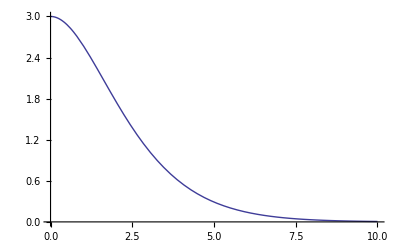

```mathematica
Plot[ⅇ^-rr (3+rr (3+rr)),{rr,0,10}]
```

```mathematica
genFnI[{1,1,0,0},{0,1,0,1}]
```

ⅈ c (-1+y)^2 y^2 (-ⅈ k[2,λ] rr[z]+ⅈ k[1,λ] rr[x]^2 rr[z])

```mathematica
Clear[g,gg]
```

```mathematica
Integrate[x^(ccc-j-1)Exp[-x],x]
```

-Gamma[ccc-j,x]

```mathematica
modBesselK[3,x]//Expand
```

15+15 x+6 x^2+x^3

```mathematica
evalEq[{1,1,0,0},{0,1,0,1}]
```

1/30 c ⅇ^(-c rr) (3+c rr (3+c rr)-(1+c rr) rr[x]^2) rr[z]

```mathematica
evalNeq[{1,1,0,0},{0,1,0,1}]
```

1/((c^2-d^2)^5)2 c (d^4 g[2,1]+2 d^6 g[2,1]+d^8 g[2,1]-2 d^2 g[2,3]-6 d^4 g[2,3]-4 d^6 g[2,3]+g[2,5]+6 d^2 g[2,5]+6 d^4 g[2,5]-2 g[2,7]-4 d^2 g[2,7]+g[2,9]-d^4 g[1,1] rr[x]^2-2 d^6 g[1,1] rr[x]^2-d^8 g[1,1] rr[x]^2+2 d^2 g[1,3] rr[x]^2+6 d^4 g[1,3] rr[x]^2+4 d^6 g[1,3] rr[x]^2-g[1,5] rr[x]^2-6 d^2 g[1,5] rr[x]^2-6 d^4 g[1,5] rr[x]^2+2 g[1,7] rr[x]^2+4 d^2 g[1,7] rr[x]^2-g[1,9] rr[x]^2) rr[z]

```mathematica
Clear[f];
f/:Dt[f,x_]:=g[x];
Dt[3f+f^2,y]
```

3 g[y]+2 f g[y]

```mathematica
Clear[f];
Derivative[1][f]^:=g;
D[3f[y]+(f[y])^2,y]
```

3 g[y]+2 f[y] g[y]

```mathematica
Derivative[1][f]^:=g//FullForm
```

```mathematica
Clear[f];
Derivative[1,0][f]^:=g;
D[3f[y,q]-f[w,y]+(f[y,q])^2,y]
```

3 g[y,q]+2 f[y,q] g[y,q]-f^(0,1)[w,y]

```mathematica
Clear[f];
Derivative[1,0][f]^:=Composition[g,First,List]
D[3f[y,q]-f[w,y]+(f[y,q])^2,y]
```

3 g[y]+2 f[y,q] g[y]-f^(0,1)[w,y]

```mathematica
Clear[f];
Derivative[1,0][f]^:=f[z,Last[{#}]]&
D[3f[y,q]-f[w,y]+(f[y,q])^2,y]
```

3 f[z,y]+2 f[y,q] f[z,y]-f^(0,1)[w,y]

```mathematica
?DSolve
```

DSolve[eqn,y,x] solves a differential equation for the function y, with independent variable x. 
DSolve[{eqn_1,eqn_2,…},{y_1,y_2,…},x] solves a list of differential equations. 
DSolve[eqn,y,{x_1,x_2,…}] solves a partial differential equation.

```mathematica
r*m*D[r*m^2+m^3,m]
```

3 m^2+2 m r

```mathematica
r/ll*#-(1/ll)*D[#,ll]&[r/ll^2+1/ll^3]//Expand
```

3/ll^5+(3 r)/ll^4+r^2/ll^3

```mathematica
D[1/ll,ll]
```

-1/ll^2

```mathematica
?Exponent
```

RowBox[{"Exponent", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["form", "TI"]}], "]"}] gives the maximum power with which StyleBox["form", "TI"] appears in the expanded form of StyleBox["expr", "TI"]. 
RowBox[{"Exponent", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["form", "TI"], ",", StyleBox["h", "TI"]}], "]"}] applies StyleBox["h", "TI"] to the set of exponents with which StyleBox["form", "TI"] appears in StyleBox["expr", "TI"].

```mathematica
(r+2*Exponent[#,r]+1)*#-r*D[#,r]&[1]//Expand
(r+2*Exponent[#,r]+1)*#-r*D[#,r]&[%]//Expand
(r+2*Exponent[#,r]+1)*#-r*D[#,r]&[%]//Expand
```

1+r

3+3 r+r^2

15+15 r+6 r^2+r^3

```mathematica
Table[sbKappa[n,x],{n,0,3}]
```

{1,1+x,3+3 x+x^2,15+15 x+6 x^2+x^3}

```mathematica
blerg[n_]:=(r+2n+1)*kk[n,r]-r*D[kk[n,r],r]-kk[n+1,r];
Collect[a*blerg[n]+b*blerg[n-1],kk[_,r]]
```

b (1+2 (-1+n)+r) kk[-1+n,r]+(-b+a (1+2 n+r)) kk[n,r]-a kk[1+n,r]-b r kk^(0,1)[-1+n,r]-a r kk^(0,1)[n,r]

```mathematica
-D[blerg[n],r]//Expand
```

-kk[n,r]-2 n kk^(0,1)[n,r]-r kk^(0,1)[n,r]+kk^(0,1)[1+n,r]+r kk^(0,2)[n,r]

```mathematica
Sum[
((n+j)!*x^(n-j))/((n-j)!*j!*2^j),
{j,0,n}]
```

ⅇ^x √(2/π) x^(1/2+n) BesselK[1/2+n,x]